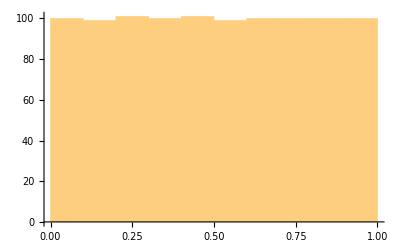

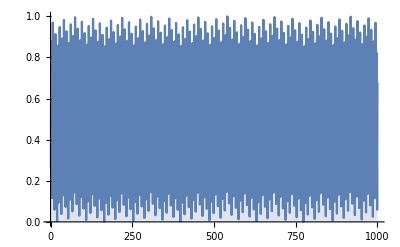

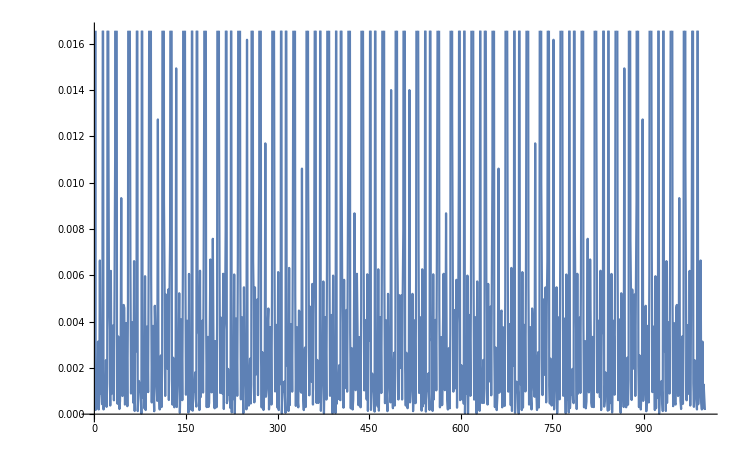

```mathematica
a=RandomReal[];
values=Table[a+=GoldenRatio ;
FractionalPart[a],1000];
Histogram[values]
ListLinePlot[values, Filling->Axis]
ListLinePlot[PeriodogramArray[values]]
```

```mathematica
img=ColorSeparate[Import["Data/bluenoise256.png"],"R"]
```

Import::nffil: File not found during Import.

ColorSeparate::imginv: Expecting an image or graphics instead of $Failed.

ColorSeparate[$Failed,R]

```mathematica
imagedata=ImageData[img];
avg=imagedata;
Table[
imagedata+=GoldenRatio;
imagedata=FractionalPart[imagedata];
{avg+=imagedata;Image[imagedata],ImagePeriodogram[Image[imagedata]]},7]
avg/=8;
Image[avg]
ImagePeriodogram[Image[avg]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

-Graphics-

-Graphics-

```mathematica
avg=ImageData[RandomImage[1,{512,512}]];
Table[
imagedata=ImageData[RandomImage[1,{512,512}]];
{avg+=imagedata;Image[imagedata],ImagePeriodogram[Image[imagedata]]},7]
avg/=8;
Image[avg]
ImagePeriodogram[Image[avg]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

-Graphics-

-Graphics-

-Graphics-

```mathematica
Slider[Dynamic[n],{1,32,1}]
Dynamic[a=RandomReal[0];
values=Table[a+=GoldenRatio ;
FractionalPart[a],n];
NumberLinePlot[values]]
```

```mathematica
img=ColorSeparate[Import["C:/Users/KAJAJJJ/Pictures/bluenoise256.png"],"R"]
```

-Graphics-